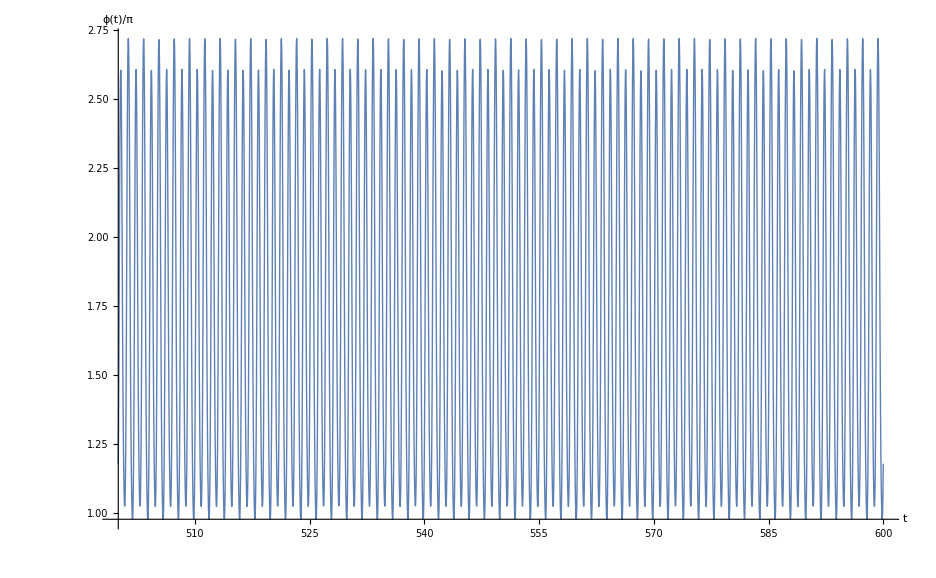

```mathematica
(*Define Variables*)
Omega=2*Pi;   (*Driving Frequency*)
omega=Omega*1.5; (* natural frequency*)
lambda = omega/2; (*Damping coefficient*)
gamma=1.077;(*Driving strength, in units of omega^2*)
(*Solve ODE using NDSolve*)
ss=NDSolve[{y''[t]+lambda*y'[t]+(omega)^2*Sin[y[t]]==gamma*(omega)^2*Cos[Omega*t],y[0]==0,y'[0]==0.15},y,{t,0,600}];
Plot[Evaluate[y[t]/.ss]/Pi,{t,500,600},PlotStyle->{Thick},AxesLabel->{"t","ϕ(t)/π"},LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
(*Check values at integer times*)
tmin=500;
tmax=600;
Table[Evaluate[y[t]/.ss][[1]],{t,tmin,tmax}]
```

{7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453,7.56184,7.05175,13.7453}

```mathematica
tmin=500;
tmax=600;
gammamin=0.3;
gammamax=0.3003;
dgamma=0.0001;
gammalist=Range[gammamin,gammamax,dgamma];
f[gamma0_]:=Module[{gamma=gamma0},
ss=NDSolve[{y''[t]+2*lambda*y'[t]+(omega)^2*Sin[y[t]]==gamma*(omega)^2*Cos[Omega*t],y[0]==0,y'[0]==0},y,{t,0,tmax}];
Table[{gamma,Mod[Evaluate[y[t]/.ss][[1]]+Pi,2Pi]-Pi},{t,tmin,tmax}]
];

f[1.07]
```